# Dos VdP con acoplo disipativo, solo en la representación de fase

Estado estacionario de dos VdP cuánticos con γc 𝒟[a1 + a2], resuelto sin pasar por Fock: ni matrices ρnm ni corte en el número de niveles d. Convenios de las notas: κp 𝒟[a_j†] + κm 𝒟[a_j.b2] en cada oscilador, r = κp/κm, y c = γc/κp para el acoplo. El núcleo de dos osciladores es K(θ1, θ2; θ1', θ2'). Con centro y diferencia en cada oscilador se separa en sectores (k1, k2), y la carga total k1 + k2 se conserva. El estacionario vive en el bloque de carga total 0, sectores (k, −k): K = Σ_k e^{−ik Θrel} K_{k,−k}(φ1, φ2). Con z_j = e^{−iφ_j} cada sector es una función B_k(z1, z2) que cumple una EDP sin raíces.

Pasos: (1) la ecuación sale del diccionario de fase del paquete; (2) herramientas para pasar de B a K y a la distribución de la fase relativa; (3) los límites con solución cerrada; (4) la solución numérica para r = 0.05 como serie en r. En cada orden de r la solución es un polinomio exacto en z1, z2: su grado lo da el orden, no se elige.

## 0. Paquete y operadores

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "RepresentacionFase.wl"}]]
```

El núcleo se escribe como polinomio en u_j = e^{−iθ_j} y v_j = e^{iθ_j'}. Cada operador es una lista de términos {coeficiente, monomio}, y un monomio, una lista {{op, j}, …} leída como producto (a o ad, oscilador j). H = Δ1 a1†a1 + Δ2 a2†a2 en el marco rotante común.

```mathematica
vars = {{u1, v1}, {u2, v2}};
H = {{Δ1, {{ad, 1}, {a, 1}}}, {Δ2, {{ad, 2}, {a, 2}}}};
saltos = {{κp, {{1, {{ad, 1}}}}}, {κp, {{1, {{ad, 2}}}}},
   {κm, {{1, {{a, 1}, {a, 1}}}}}, {κm, {{1, {{a, 2}, {a, 2}}}}},
   {γc, {{1, {{a, 1}}}, {1, {{a, 2}}}}}};
rval = 1/20;
```

## 1. La ecuación, desde el diccionario de fase

lindbladFase2 aplica las reglas (41)–(42) de las notas a cada oscilador en su par de variables (aρ → e^{iθ}√D_θ K, …), sin truncar. Se aplica a un núcleo cualquiera del bloque de carga total 0, con coeficientes libres s[n1, m1, n2, m2]:

```mathematica
pK = Sum[If[n1 - m1 + n2 - m2 == 0, s[n1, m1, n2, m2] u1^n1 v1^m1 u2^n2 v2^m2, 0],
   {n1, 0, 3}, {m1, 0, 3}, {n2, 0, 3}, {m2, 0, 3}];
dpK = lindbladFase2[pK, H, saltos, vars];
```

Las EDP del bloque de carga total 0 para B_k ≡ B_{k,−k}(z1, z2). El operador local de cada oscilador es el de un oscilador con la pérdida simple que trae 𝒟[a1 + a2]; el acoplo junta cada sector con sus vecinos k ± 1 (w = (z1 + z2)/2):

```mathematica
Lloc[k_, z_][f_] := κp (z (z - 1) D[f, z] + ((k + 1) z - k/2 - 1) f) +
   κm ((1 - z^2) D[f, {z, 2}] - k z D[f, z] - k (k - 1)/2 f) + γc ((1 - z) D[f, z] - k/2 f);
w = (z1 + z2)/2;
edp[B_, k_] := Lloc[Abs[k], z1][B[k]] + Lloc[Abs[k], z2][B[k]] - I (Δ1 - Δ2) k B[k] +
   If[k == 0, γc (1 - w) (B[1] + B[-1]),
    γc (1 - w) B[k + Sign[k]] +
     γc ((1 - w) D[B[k - Sign[k]], z1, z2] - Abs[k]/2 (D[B[k - Sign[k]], z1] + D[B[k - Sign[k]], z2]))];
```

Comprobación: los sectores de ∂t K (del diccionario) pasados a z con generatriz2 son las EDP aplicadas a los sectores de K. Tiene que dar ceros:

```mathematica
Bp[k_] := generatriz2[pK, {k, -k}, vars, {z1, z2}];
Table[Simplify[generatriz2[dpK, {k, -k}, vars, {z1, z2}] - edp[Bp, k]], {k, -2, 2}]
```

{0,0,0,0,0}

## 2. De B a K y a la distribución de fase

Con osciladores idénticos y sin desintonía el estacionario cumple B_{−k} = B_k (intercambio y hermiticidad), así que basta la lista Bs = {B_0, B_1, B_2, …}. sectorDesdeGeneratriz2 deshace los pesos y da K_{k,−k}(φ1, φ2). En la diagonal (φ1 = φ2 = 0) queda c_k = K_{k,−k}(0, 0), y la distribución de la fase relativa es P(Θrel) = (1/2π) Σ_k c_k e^{−ikΘrel}. El núcleo que queda depende de Θrel, φ1 y φ2; se dibuja |K| en el corte φ1 = φ2 = φ.

```mathematica
sectorK[B_, k_] := sectorDesdeGeneratriz2[Expand[B], {k, -k}, {z1, z2}, {φ1, φ2}];
crel[Bs_, k_] := sectorK[Bs[[k + 1]], k] /. {φ1 -> 0, φ2 -> 0};
Prel[Bs_] := (1 + 2 Sum[crel[Bs, k] Cos[k Θrel], {k, 1, Length[Bs] - 1}])/(2 Pi);
nucleoRel[Bs_] := sectorK[Bs[[1]], 0] + 2 Sum[Cos[k Θrel] sectorK[Bs[[k + 1]], k], {k, 1, Length[Bs] - 1}];
```

```mathematica
ejes = {{Range[0, 2 Pi, Pi/2], None}, {Range[0, 2 Pi, Pi/2], None}};
dibujarP[curvas_, etiquetas_, opts___] := Plot[Evaluate[curvas], {Θrel, 0, 2 Pi}, opts,
   PlotLegends -> etiquetas, Frame -> True, FrameLabel -> {"Θrel", "P(Θrel)"},
   FrameTicks -> {{Automatic, None}, {Range[0, 2 Pi, Pi/2], None}}];
dibujarK[nucleo_, titulo_] := DensityPlot[Evaluate[Abs[nucleo /. {φ1 -> φ, φ2 -> φ}]],
   {Θrel, 0, 2 Pi}, {φ, 0, 2 Pi}, PlotPoints -> 40, ColorFunction -> "SunsetColors",
   FrameLabel -> {"Θrel", "φ1 = φ2 = φ"}, FrameTicks -> ejes, PlotLabel -> titulo,
   PlotLegends -> Automatic, ImageSize -> 300];
```

Para dibujar una solución cerrada (no polinómica) hay que pasar de B a K coeficiente a coeficiente. Se usa la serie de Kummer, M(1, b, y) = Σ y^m/(b)_m, sumada hasta que los términos son despreciables (< 10^-25 con r = 0.05). No es un corte de la dinámica: es evaluar una función entera conocida.

```mathematica
Gk[b_, y_] := Hypergeometric1F1[1, b, b (1 + y)]/Hypergeometric1F1[1, b, 2 b];
GkPol[b_, y_, mmax_: 40] := Sum[(b (1 + y))^m/Pochhammer[b, m], {m, 0, mmax}]/Hypergeometric1F1[1, b, 2 b];
```

## 3. Límites con solución cerrada

### 3.1 Sin acoplo (γc = 0)

Todo se separa: G(z1, z2) = G(z1) G(z2) y B_k = 0 para k ≠ 0. Cada factor es el Kummer de un oscilador, porque con γc = 0 el operador local de k = 0 tiene el factor (1 − z). Tiene que dar 0:

```mathematica
Simplify[(Lloc[0, z][g[z]] /. γc -> 0) - (1 - z) (κm (1 + z) g''[z] - κp D[z g[z], z])]
```

0

Por tanto Lloc^(0)_1 + Lloc^(0)_2 aplicado a G(z1) G(z2) da G(z2) (Lloc G)(z1) + G(z1) (Lloc G)(z2) = 0 si cada factor es Kummer. Con r = 0.05, residuo de la EDO de Kummer en un punto cualquiera (tiene que dar ≈ 0):

```mathematica
With[{y = 0.3 + 0.2 I}, N[((1 + z) D[Gk[rval, z], {z, 2}] - rval D[z Gk[rval, z], z]) /. z -> y, 20]]
```

-6.245×10^-17-7.54605×10^-17 ⅈ

La fase relativa es uniforme, P = 1/2π. El núcleo es K_{0,0} = G(e^{−iφ1}) G(e^{−iφ2}): no depende de Θrel (bandas horizontales). Toda la información está en φ, como con un oscilador:

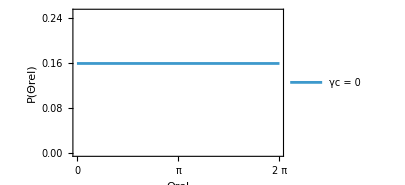
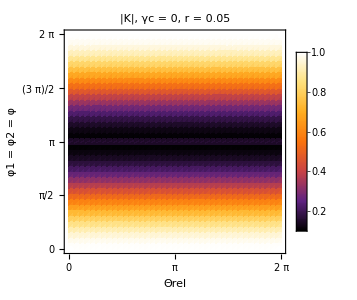

```mathematica
K0sinAcoplo = Gk[rval, Exp[-I φ1]] Gk[rval, Exp[-I φ2]];
Row[{dibujarP[{1/(2 Pi)}, {"γc = 0"}, PlotRange -> {0, 0.25}, ImageSize -> 300],
  dibujarK[K0sinAcoplo, "|K|, γc = 0, r = 0.05"]}]
```

### 3.2 Acoplo fuerte (γc ≫ κm, κp)

𝒟[a1 + a2] deja el modo a1 + a2 en el vacío y queda a1 − a2, un VdP con la mitad de pérdida doble. Hace falta γc mayor que κp y también que κm: si no, la ganancia sigue metiendo excitaciones en a1 + a2 y la pérdida doble las vacía junto con una de a1 − a2, antes de que γc las quite (es lo que pasa en 3.4 con c → ∞). En las EDP: con el ansatz B_k = (−1/2)^|k| F^(|k|)(w), w = (z1 + z2)/2, todo lo que multiplica a γc se anula para cualquier F. Tiene que dar ceros:

```mathematica
Bfuerte[k_] := (-1/2)^Abs[k] Derivative[Abs[k]][F][w];
Table[Simplify[Coefficient[Expand[edp[Bfuerte, k] /. {Δ1 -> 0, Δ2 -> 0}], γc]], {k, 0, 4}]
```

{0,0,0,0,0}

F la fija el orden siguiente. Con B = B⁽⁰⁾ + B⁽.b9⁾/γc + …, el orden γc⁰ es Lγ B⁽.b9⁾ + L1 B⁽⁰⁾ = 0: Lγ es lo que multiplica a γc en edp y L1 es lo que queda (κp y κm). Si una función lineal de los B_k se anula sobre Lγ X para cualquier X (algo que γc conserva), al aplicarla a esa ecuación queda que también se anula sobre L1 B⁽⁰⁾. Esa función es la generatriz del modo a1 − a2, escrita con los sectores:

proyeccion[B](y) = Σ_k Σ_j (−(y − 1)/2)^(2j+|k|) / (j! (j + |k|)!) ∂1^j ∂2^j B_k, en z1 = z2 = (1 + y)/2.

Hay que comprobar tres cosas: (i) sobre el ansatz devuelve F; (ii) proyeccion[Lγ B] = 0 para cualquier B; (iii) proyeccion[L1 B⁽⁰⁾] es el operador de un solo VdP aplicado a F, con κm → κm/2. Primero con polinomios genéricos de coeficientes libres, donde las sumas son finitas. Tiene que dar tres ceros:

```mathematica
proyeccion[B_, kmax_, jmax_] := Sum[(-(y - 1)/2)^(2 j + Abs[k])/(j! (j + Abs[k])!) (D[B[k], {z1, j}, {z2, j}] /. {z1 -> (1 + y)/2, z2 -> (1 + y)/2}), {k, -kmax, kmax}, {j, 0, jmax}];
sinDes = {Δ1 -> 0, Δ2 -> 0};
Fpol = Sum[f[n] y^n, {n, 0, 6}];
Bans[k_] := (-1/2)^Abs[k] (D[Fpol, {y, Abs[k]}] /. y -> w);
Bgen[k_] := If[Abs[k] > 3, 0, Sum[x[k, i, l] z1^i z2^l, {i, 0, 3}, {l, 0, 3}]];
LgBgen[k_] := Coefficient[Expand[edp[Bgen, k] /. sinDes], γc];
L1Bans[k_] := Expand[edp[Bans, k] /. sinDes /. γc -> 0];
{Expand[proyeccion[Bans, 6, 6] - Fpol], Expand[proyeccion[LgBgen, 4, 8]],
 Expand[proyeccion[L1Bans, 6, 14] - (1 - y) (κm/2 (1 + y) D[Fpol, {y, 2}] - κp D[y Fpol, y])]}
```

{0,0,0}

Ahora para cualquier F, no solo polinomios. Todo es lineal en F, así que basta F = e^(λy): sus derivadas en λ = 0 son las potencias y^n. La suma doble en (j, k) es la suma sobre dos enteros libres p, q ≥ 0, con j = min(p, q) y j + |k| = max(p, q). El sumando sale simétrico en (p, q) (primera salida, True) y la suma se separa en Σ_p p^m x^p/p! = e^x BellB[m, x]. Las otras dos salidas son (i), dividida por e^(λy), y la diferencia de (iii). Tiene que dar {True, 1, 0}:

```mathematica
Module[{lam, Q, R, sumaPQ, p, q, xx, j, k, a, c, zz = {z1 -> (1 + y)/2, z2 -> (1 + y)/2}},
 Q = Expand[Simplify[(Lloc[k, z1][Exp[lam w]] + Lloc[k, z2][Exp[lam w]] /. γc -> 0)/Exp[lam w]]];
 R[pol_] := Module[{m1, m2}, Expand[Simplify[Total[(#[[2]] D[m1^j m2^j Exp[m1 z1 + m2 z2], {m1, #[[1, 1]]}, {m2, #[[1, 2]]}]) & /@
        CoefficientRules[pol, {z1, z2}]]/(m1^j m2^j Exp[m1 z1 + m2 z2])] /. {m1 -> lam/2, m2 -> lam/2} /. zz]];
 sumaPQ[pol_] := Module[{s = Expand[pol /. {k -> q - p, j -> p}]},
   {Expand[s - (s /. {p -> q, q -> p})] === 0,
    Exp[2 xx + lam (1 + y)/2] (s /. {p^m_. q^n_. :> BellB[m, xx] BellB[n, xx]} /. {p^m_. :> BellB[m, xx], q^n_. :> BellB[n, xx]}) /. xx -> (y - 1) lam/4}];
 a = sumaPQ[R[1]]; c = sumaPQ[R[Q]];
 {a[[1]] && c[[1]], Simplify[a[[2]]/Exp[lam y]],
  Simplify[c[[2]] - (1 - y) (κm/2 (1 + y) D[Exp[lam y], {y, 2}] - κp D[y Exp[lam y], y])]}]
```

(ii) para cualquier B: basta B_k = e^(m1 z1 + m2 z2) en un solo sector k0. Con k0 = 0 las salidas se sacan directamente de edp. Con k0 ≥ 1, lo que multiplica a γc cae en los sectores k0 − 1, k0 y k0 + 1: se comprueba que esas tres salidas coinciden con edp para k0 = 1, …, 5 y se suman con k0 simbólico (sale una combinación de BesselI que se anula). Los sectores negativos dan lo mismo, porque edp solo depende de |k|. Tiene que dar {0, {0}, 0}:

```mathematica
Module[{m1, m2, n1, n2, e, piSector, Bin, salidas, k0, j, cero, comprobacion, general},
 e = Exp[m1 z1 + m2 z2];
 piSector[expr_, kk_] := Sum[(-(y - 1)/2)^(2 j + kk)/(j! (j + kk)!) Total[(#[[2]] D[n1^j n2^j Exp[n1 z1 + n2 z2], {n1, #[[1, 1]]}, {n2, #[[1, 2]]}]) & /@
        CoefficientRules[Expand[expr/e], {z1, z2}]] /. {n1 -> m1, n2 -> m2}, {j, 0, Infinity}] /. {z1 -> (1 + y)/2, z2 -> (1 + y)/2};
 Bin[k0_][kk_] := If[kk == k0, e, 0];
 cero = FullSimplify[Sum[piSector[Coefficient[Expand[edp[Bin[0], kk] /. sinDes], γc], Abs[kk]], {kk, -1, 1}], m1 > 0 && m2 > 0 && y > 1];
 salidas[k0_] := {(1 - w) e, Coefficient[Expand[Lloc[k0, z1][e] + Lloc[k0, z2][e]], γc],
    (1 - w) D[e, z1, z2] - (k0 + 1)/2 (D[e, z1] + D[e, z2])};
 comprobacion = Union[Flatten[Table[Expand[Table[Coefficient[Expand[edp[Bin[n], kk] /. sinDes], γc], {kk, n - 1, n + 1}] - salidas[n]], {n, 1, 5}]]];
 general = FullSimplify[Total[MapThread[piSector, {salidas[k0], {k0 - 1, k0, k0 + 1}}]],
    m1 > 0 && m2 > 0 && y > 1 && k0 >= 1 && Element[k0, Integers]];
 {cero, comprobacion, general}]
```

La condición que queda para F es (1 − y)[(κm/2)(1 + y) F'' − κp (y F)'] = 0: el operador local de k = 0 de un oscilador (3.1) con κm → κm/2, es decir, r → 2r. Su solución es el Kummer G_{2r}. Tiene que dar 0:

```mathematica
Simplify[(1 + y) D[Gk[2 r, y], {y, 2}] - 2 r D[y Gk[2 r, y], y]]
```

La corrección es el orden siguiente, ∝ 1/γc. Con r = 0.05:

```mathematica
Ffuerte = GkPol[2 rval, y];
BsFuerte = Table[Expand[(-1/2)^k D[Ffuerte, {y, k}] /. y -> w], {k, 0, 6}];
Table[N[crel[BsFuerte, k]], {k, 1, 4}]
```

c_1 < 0: el máximo de P está en Θrel = π (antifase). ⟨a2† a1⟩ = B_1(1, 1) = −n̄_{2r}/2:

```mathematica
{N[BsFuerte[[2]] /. {z1 -> 1, z2 -> 1}], -N[D[Ffuerte, y] /. y -> 1]/2}
```

```mathematica
Row[{dibujarP[{Prel[BsFuerte]}, {"γc ≫ κm"}, PlotRange -> {0, 0.25}, ImageSize -> 300],
  dibujarK[nucleoRel[BsFuerte], "|K|, γc ≫ κm, r = 0.05"]}]
```

### 3.3 Acoplo fuerte (γc ≫ κm) con κm = 2κp: todo explícito

Con κm = 2κp es 2r = 1 y el Kummer es una exponencial: G_1(y) = e^{y−1}. Tiene que dar e^{y−1}:

```mathematica
Simplify[Gk[1, y]]
```

Así que G = e^{w−1} y B_k = (−1/2)^k e^{w−1}: el anillo coherente en antifase, |α1|.b2 = |α2|.b2 = 1/2 y α2 = −α1. Los c_k salen de una suma que converge muy deprisa, c_k = (−1/2)^k e^{−1} (Σ_n 2^{−n}/√(n!(n + k)!)).b2; se compara con el paso coeficiente a coeficiente (tiene que dar ≈ 0):

```mathematica
BsExp = Table[Expand[(-1/2)^k Normal[Series[Exp[y - 1], {y, 0, 40}]] /. y -> w], {k, 0, 6}];
cExp[k_] := (-1/2)^k Exp[-1] Sum[2^-n/Sqrt[n! (n + k)!], {n, 0, 60}]^2;
Table[N[crel[BsExp, k] - cExp[k], 15], {k, 1, 4}]
```

```mathematica
Row[{dibujarP[{Prel[BsExp]}, {"κm = 2κp, γc ≫ κm"}, PlotRange -> {0, 0.4}, ImageSize -> 300],
  dibujarK[nucleoRel[BsExp], "|K|, κm = 2κp, γc ≫ κm"]}]
```

### 3.4 Límite cuántico (r → 0 con c = γc/κp fijo)

Con κm = 1, κp = r y γc = c r, el lindbladiano es L− + r (L+ + c Lγ). La pérdida doble L− tiene modos cero (1, z1, z2, z1 z2 en G; la constante en B_1), y sus coeficientes los fija el orden siguiente. Por eso resolverSerie[M, c] resuelve a la vez los órdenes 0, …, M de la serie en r y devuelve los 0, …, M − 1, que ya están fijados. Cada orden es un polinomio exacto en z1, z2 (grado ≤ orden + 2, sectores |k| ≤ M + 1): no hay ningún corte que elegir. c puede ser simbólico o un número exacto:

```mathematica
resolverSerie[M_, cv_] := Module[{Kmax = M + 1, P, B, ecs, inc, sol, grado},
  grado[o_] := o + 2;
  P[k_, o_] := Sum[x[k, o, i, j] z1^i z2^j, {i, 0, grado[o]}, {j, 0, grado[o]}];
  B[k_] := If[Abs[k] > Kmax, 0, Sum[r^o P[Abs[k], o], {o, 0, M}]];
  inc = Flatten[Table[x[k, o, i, j], {k, 0, Kmax}, {o, 0, M}, {i, 0, grado[o]}, {j, 0, grado[o]}]];
  ecs = Flatten[Table[
     With[{res = Expand[edp[B, k] /. {κp -> r, κm -> 1, γc -> cv r, Δ1 -> 0, Δ2 -> 0}]},
      Table[Flatten[CoefficientList[Coefficient[res, r, o], {z1, z2}]], {o, 0, M}]], {k, 0, Kmax}]];
  ecs = Join[ecs, {(P[0, 0] /. {z1 -> 1, z2 -> 1}) - 1}, Table[P[0, o] /. {z1 -> 1, z2 -> 1}, {o, 1, M}]];
  sol = Quiet[Solve[Thread[ecs == 0], inc], Solve::svars];
  Table[Expand[Sum[r^o P[k, o], {o, 0, M - 1}] /. First[sol]], {k, 0, Kmax}]]
```

El orden r^0, exacto en c:

```mathematica
BsC = resolverSerie[2, c];
BsCuant = Simplify[BsC /. r -> 0];
{Collect[BsCuant[[1]], {z1, z2}, Factor], Factor[BsCuant[[2]]], BsCuant[[3]]}
```

El primer armónico y su desarrollo en el acoplo:

```mathematica
{Factor[crel[BsCuant, 1]], Series[crel[BsCuant, 1], {c, 0, 3}]}
```

c → ∞ aquí es κp ≪ γc ≪ κm, y no da el acoplo fuerte de 3.2 (que sería (2 + w)/3 y B_1 = −1/6). Sale G → 3/4 + (z1 + z2)/8 y B_1 → −1/8: en kets, |00〉 con peso 3/4 y la antifase (|10〉 − |01〉)/√2 con 1/4. a1 + a2 la aniquila, así que γc no la toca; la ganancia la saca de ahí a ritmo 3κp (2κp hacia |2〉 de a1 − a2 y κp hacia una excitación de a1 + a2, que la pérdida doble vacía enseguida), y la llena desde |00〉 a ritmo κp:

```mathematica
BsOscuro = Limit[BsCuant, c -> Infinity];
{Expand[BsOscuro[[1]]], BsOscuro[[2]]}
```

```mathematica
Row[{dibujarP[Table[Prel[BsCuant /. c -> cv], {cv, {1/5, 1, 5}}], {"c = 0.2", "c = 1", "c = 5"}, PlotRange -> {0.1, 0.22}, ImageSize -> 300],
  dibujarK[nucleoRel[BsCuant /. c -> 1], "|K|, límite cuántico, c = 1"]}]
```

## 4. Numérico: r = 0.05 como serie en r

Por qué con c = γc/κp fijo: en el límite cuántico las poblaciones dependen de γc/κp (ganancia contra pérdida simple), así que desarrollar por separado en γc y en r no tiene sentido. Se desarrolla en r con c fijo; el acoplo entra exacto en cada orden, y su desarrollo en c es el de 3.4. Se resuelve hasta el orden 5 en r (unos 15 s por valor de c) para tres acoplos:

```mathematica
ordenMax = 5;
valoresC = {1/5, 1, 5};
serie = AssociationMap[resolverSerie[ordenMax + 1, #] &, valoresC];
truncar[Bs_, o_] := Normal[Series[Bs, {r, 0, o}]];
```

Convergencia: c_1, c_2 y ⟨a2† a1⟩ = B_1(1, 1) con r = 0.05, cortando la serie en cada orden. La diferencia entre dos órdenes seguidos da el error:

```mathematica
Table[TableForm[Table[With[{b = N[truncar[serie[cv], o] /. r -> rval]}, {o, crel[b, 1], crel[b, 2], b[[2]] /. {z1 -> 1, z2 -> 1}}], {o, 0, ordenMax}],
   TableHeadings -> {None, {"orden", "c1", "c2", "⟨a2† a1⟩"}}, TableDepth -> 2] // Labeled[#, "c = " <> ToString[cv, InputForm], Top] &, {cv, valoresC}]
```

Desarrollo en el acoplo del orden r^1 de c_1 (exacto en c):

```mathematica
c1orden1 = Factor[Coefficient[crel[BsC, 1], r, 1]];
{c1orden1, Series[c1orden1, {c, 0, 2}]}
```

Con c = 0.2 y c = 1 la serie converge a ~10^-5 en el orden 5. Con c = 5 converge más despacio (γc = 0.25 κm) y el error es ~10^-3.

Distribución de la fase relativa con r = 0.05 para los tres acoplos, con las dos referencias de acoplo grande: κp ≪ γc ≪ κm (estado oscuro de 3.4, punto y raya) y γc ≫ κm (3.2, discontinua). El máximo está siempre en Θrel = π: antifase. c = 5 (γc = 0.25 κm) ya está cerca del estado oscuro; para llegar a 3.2 haría falta c ≫ 1/r = 20:

```mathematica
BsNum = N[serie[#] /. r -> rval] & /@ valoresC;
dibujarP[Join[Prel /@ BsNum, {Prel[BsOscuro], Prel[BsFuerte]}], {"c = 0.2", "c = 1", "c = 5", "κp ≪ γc ≪ κm", "γc ≫ κm"},
  PlotStyle -> {Automatic, Automatic, Automatic, Directive[Black, DotDashed], Directive[Black, Dashed]}, PlotRange -> {0.08, 0.24}, ImageSize -> 450]
```

El núcleo que queda, |K(Θrel; φ, φ)|, para los tres acoplos. Sin acoplo serían bandas horizontales (3.1); el acoplo las modula en Θrel con el máximo en π:

```mathematica
Grid[{MapThread[dibujarK[nucleoRel[#1], "|K|, r = 0.05, c = " <> ToString[#2, InputForm]] &, {BsNum, valoresC}]}]
```

## 5. Lenguas de Arnold: osciladores con frecuencias distintas

En el marco rotante común (frecuencia ω, Δ_j = ω_j − ω) el hamiltoniano da, en el sector (k1, k2), −i(Δ1 k1 + Δ2 k2) = −i[(Δ1 + Δ2)/2 (k1 + k2) + (Δ1 − Δ2)(k1 − k2)/2]. La parte común multiplica la carga total, que en el bloque del estacionario es 0: desaparece para cualquier ω, no solo para el marco intermedio. Lo que queda es δ = Δ1 − Δ2 = ω1 − ω2, la diferencia de frecuencias propias, que no depende del marco. Con δ ≠ 0 ya no vale B_{−k} = B_k: los sectores negativos llevan sus propias incógnitas. Se mide δ en unidades de κp, como el acoplo (Δ1 − Δ2 = δ r con κm = 1):

```mathematica
resolverSerieD[M_, cv_, D1_, D2_] := Module[{Kmax = M + 1, P, B, ecs, inc, sol, grado},
  grado[o_] := o + 2;
  P[k_, o_] := Sum[x[k, o, i, j] z1^i z2^j, {i, 0, grado[o]}, {j, 0, grado[o]}];
  B[k_] := If[Abs[k] > Kmax, 0, Sum[r^o P[k, o], {o, 0, M}]];
  inc = Flatten[Table[x[k, o, i, j], {k, -Kmax, Kmax}, {o, 0, M}, {i, 0, grado[o]}, {j, 0, grado[o]}]];
  ecs = Flatten[Table[
     With[{res = Expand[edp[B, k] /. {κp -> r, κm -> 1, γc -> cv r, Δ1 -> D1 r, Δ2 -> D2 r}]},
      Table[Flatten[CoefficientList[Coefficient[res, r, o], {z1, z2}]], {o, 0, M}]], {k, -Kmax, Kmax}]];
  ecs = Join[ecs, {(P[0, 0] /. {z1 -> 1, z2 -> 1}) - 1}, Table[P[0, o] /. {z1 -> 1, z2 -> 1}, {o, 1, M}]];
  sol = Quiet[Solve[Thread[ecs == 0], inc], Solve::svars];
  Association[Table[k -> Expand[Sum[r^o P[k, o], {o, 0, M - 1}] /. First[sol]], {k, -Kmax, Kmax}]]]
```

El marco no importa: con δ = 2 κp, repartiendo la desintonía a medias (Δ1 = −Δ2 = κp) o toda en el oscilador 1 (Δ1 = 2κp, Δ2 = 0), el bloque del estacionario es el mismo. Tiene que dar ceros:

```mathematica
Simplify[Values[resolverSerieD[3, 1, 1, -1]] - Values[resolverSerieD[3, 1, 2, 0]]]
```

### 5.1 Límite cuántico: la lengua en forma cerrada

La proyección sobre los modos cero (la de 3.4) con δ ≠ 0: en la condición de B_{1,−1} entra −iδ q, y en las de G, q + q̄. Las poblaciones siguen siendo simétricas, p10 = p01 = (2 + c) p11, y la coherencia es q = γc (p11 − p10)/(3κp + γc + iδ). En el límite cuántico c_1 = q. Se compara con la serie (tiene que dar 0):

```mathematica
q0[cv_, dv_] := -cv (1 + cv) (3 + cv - I dv)/((3 + cv) (27 + 27 cv + 8 cv^2 + (3 + cv) dv^2));
Simplify[(resolverSerieD[2, 1, 1, -1][1] /. r -> 0) - q0[1, 2]]
```

|c_1| es la amplitud del primer armónico de P(Θrel). La lengua de Arnold en el plano (δ, γc), en unidades de κp: el enganche (|c_1| grande) se abre al crecer el acoplo. A acoplo fijo, |c_1| cae con δ como una lorentziana de anchura 3κp + γc = 2Γ1:

```mathematica
vmaxA = 0.13;
lenguaQ = DensityPlot[Abs[q0[cv, dv]], {dv, -15, 15}, {cv, 0, 10}, PlotPoints -> 60,
   ColorFunction -> (ColorData["SunsetColors"][#/vmaxA] &), ColorFunctionScaling -> False,
   FrameLabel -> {"δ/κp", "γc/κp"}, PlotLabel -> "|c1|, límite cuántico", ImageSize -> 360];
Legended[lenguaQ, BarLegend[{"SunsetColors", {0, vmaxA}}]]
```

Con δ ≠ 0, c_1 deja de ser real y el pico de P(Θrel) se desplaza de π a Θrel = arg c_1 = π − arctan(δ/(3κp + γc)), a la vez que se aplana. P(Θrel) = (1 + 2 Re(c_1 e^{−iΘrel}))/2π con γc = κp:

```mathematica
Plot[Evaluate[Table[(1 + 2 Re[q0[1, dv] Exp[-I Θrel]])/(2 Pi), {dv, {0, 3, 8}}]], {Θrel, 0, 2 Pi},
  PlotLegends -> {"δ = 0", "δ = 3κp", "δ = 8κp"}, Frame -> True, FrameLabel -> {"Θrel", "P(Θrel)"},
  FrameTicks -> {{Automatic, None}, {Range[0, 2 Pi, Pi/2], None}}, PlotRange -> {0.14, 0.18}, ImageSize -> 400]
```

### 5.2 r = 0.05

La serie en r hasta el orden 3 (unos 4 s por punto) para unos valores de δ y los tres acoplos, frente al límite cuántico (líneas). |c_1| es par en δ (δ → −δ conjuga c_1), así que basta δ ≥ 0:

```mathematica
valoresD = {0, 1, 2, 3, 4, 6, 8, 11, 15};
c1Arnold = Table[{dv, Abs[N[crel[Values[KeySort[KeySelect[resolverSerieD[4, cv, dv/2, -dv/2], # >= 0 &]]], 1] /. r -> rval]]}, {cv, valoresC}, {dv, valoresD}];
Show[ListPlot[c1Arnold, PlotLegends -> {"c = 0.2", "c = 1", "c = 5"}, PlotMarkers -> Automatic],
  Plot[Evaluate[Table[Abs[q0[cv, dv]], {cv, valoresC}]], {dv, 0, 15}, PlotStyle -> Dashed],
  Frame -> True, FrameLabel -> {"δ/κp", "|c1|"}, PlotRange -> {0, 0.13}, ImageSize -> 420]
```